# EOM Sideband Modulation

#### Intensity amplitude, relative to the input amplitude of the the m^th sideband frequency is given by |J_m(η)|^2, where η = -(1/2)rn^3 k_0 n_0 LV_0/w for V_o applied across a crystal of width w and length L.

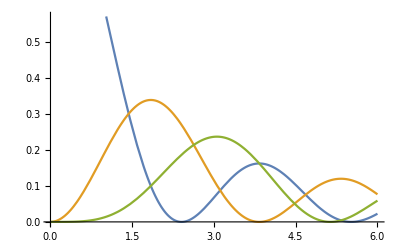

```mathematica
Plot[{BesselJ[0,η]^2,BesselJ[1,η]^2,BesselJ[2,η]^2},{η,0.001,6}]
```

For a 2W amplifier, and the modulation depth of 0.14 rad given for the 4431 Newport EOM, the peak phase shift eta is 1.066. The corresponding relative intensity per first order sideband is:

```mathematica
BesselJ[1,1.066]^2
```

0.212329